## Illustration of transient shot noise Zs. Elter

This notebook illustrates a possible solution to define transient shot noise processes with Mathematica. In order to test the Manipulate capability, there is no need to run all the code snipplets, just jump to and run the part which imports the attached .mat file.  If the user wants to set a different count rate time dependence, then one needs first to rerun the other parts as well, which can be time consuming.

### Definition of the transient

Let us define an arbritrary function of the count rate in time. In the current example the time units are defined as ns, and the count rate units as cps.

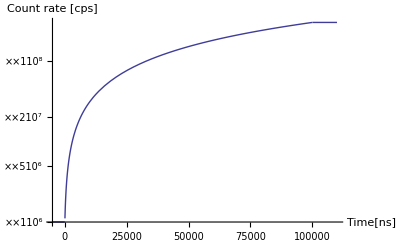

```mathematica
CountRate[t_]=Piecewise[{{10^6, t<0},{10^6+t*((3*10^8-10^6)/100000), 0≤t<100000}},3*10^8];
LogPlot[CountRate[t],{t,-5000,110000},AxesLabel->{"Time[ns]","Count rate [cps]"}]
```

### Inhomogeneous arrival times

In this example the simulation of the signal starts before the measurement (ie. the plotting, which starts at t=0) of the signal, in order to reach stationarity (for more details on stationarity or equilibrium, please refer to Zs. Elter et al. NIMA 813 pp 10 - 12 (2016)).

```mathematica
Ti=List[]; (*list containing the arrival times of each event*)
AppendTo[Ti,-10000]; 
While[Ti[[-1]]≤105000, (*in this example the length of the measurement is 105000 ns*)
Ti0=10^(9)*RandomVariate[ExponentialDistribution[CountRate[Ti[[-1]]]]]; (*Draw an exponential random number with the count rate at the previous event*)
AppendTo[Ti,Ti[[-1]]+Ti0] (*Accumulate these random numbers*)]
Ti=Select[Ti,#>0&];   (*Interested just in the events for t>0*)
```

### Pulse shape

Let us define an arbritrary function to describe the pulses. In the current example the pulses have exponential decay shape with few tens of ns width and with a deterministic amplitude of 5 μA (the amplitude units are considered in μA).

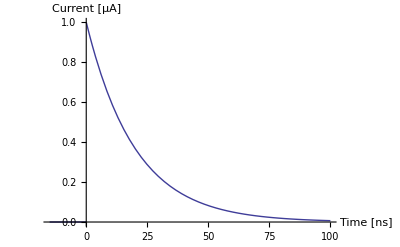

```mathematica
p= 20;                           (* pulse shape parameter, in ns units*)
ImpulseExp[t_]:=Piecewise[{{Exp[-t/p], 0≤t}},0];
AmplitudeExp=5; (*In case one wants to introduce stochastic amplitudes, just change this call to RandomVariate[dist,Length[Ti]]*)
Plot[ImpulseExp[t],{t,-15,100},AxesLabel->{"Time [ns]","Current [μA]"}]
```

### The shot noise

The signal (ie. the inhomogeneous shot noise) is considered as the sum of pulses arriving at the previously computed time arrivals. (One may plot it as it is, but the plotting can take a long time, therefore placing that line inside a comment is adviced; note that Mathematica stores this function in a closed form of the sum of several exponential functions, therefore its evaluation may take long).

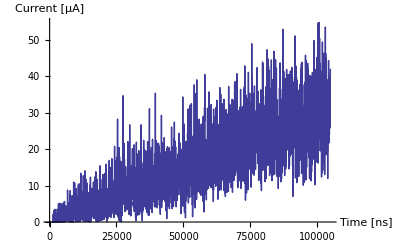

```mathematica
StProcExp[t_]:= Sum[AmplitudeExp*ImpulseExp[t-Ti[[i]]], {i,1,Length[Ti],1}] (*In case one wants to introduce stochastic amplitudes, just modify the multiplication to AmplitudeExp[[i]]*)
Plot[StProcExp[t],{t,0,105000},PlotRange->Full,AxesLabel->{"Time [ns]","Current [μA]"}]
```

### Sampling the signal

As mentioned above, the evaluation of the signal function may take long, therefore the "Manipulate" - d plotting of the continous function is not possible, hence one should sample the signal, and export the data in a file, which can be imported and used later. In the current example the sampling is done in every 8 ns (ie. 125 MHz). To create a list of the sampled values, the ParallelTable command is used in order to save computing time (if the user has problems using this functions, please modify it to Table). Still, this process may take several minutes depending on the computing power.

```mathematica
Sampling=8;              (*ns*)
MeasTime=105000;(*ns*)
StProcNum=ParallelTable[StProcExp[i],{i,0,MeasTime,Sampling}] ; 
TimeNum = ParallelTable[i,{i,0,MeasTime,Sampling}] ;
```

Let us export these data points. (In order to be sure where the data is exported, one can set a suitable path, and/or print the working directory with the Directory[] command.)

```mathematica
Export["TransientSigManip.mat",{TimeNum,StProcNum}]
```

TransientSigManip.mat

### Manipulate plot of the signal

Finally, let us create a Manipulate plot for illustration. (If one doesnt want to keep the PlotRange fixed, just modify it to Full)

```mathematica
data=Import["TransientSigManip.mat"]; (*Make sure that the file is at the working directory*)
TimeNum=data[[1]][[1]];
StProcNum=data[[1]][[2]];
```

```mathematica
MaxPlotRange=Max[StProcNum]*1.05;
Manipulate[ListPlot[Transpose@{TimeNum⟦t1;;t1+999⟧,StProcNum⟦t1;;t1+999⟧},Joined->True,PlotRange->{0,MaxPlotRange}],{t1,1,Length[StProcNum]-999,1}]
```